```mathematica
ClearAll[lengths]
```

```mathematica
ImportDataset["TrainingDataRangeValues.mx"]
```

```mathematica
lengths[[1]]
```

k[k][k][k[s]]→3

```mathematica
lengths = lengths/.(a_->b_)/;!(b===False):> (a->True);
```

```mathematica
CreateRasterizedTrainingData[var_]:=Module[{NoHalt,Halt,HaltTrain,HaltTrainRaster,NoHaltTrainRaster,RasterTrain},
NoHalt = Select[var,#[[2]]==False&];
Halt = Select[var,#[[2]]==True&];
HaltTrain = RandomSample[Halt,Length[NoHalt]];
HaltTrainRaster=Monitor[Table[SKRasterize[HaltTrain[[x,1]],5]-> HaltTrain[[x,2]],{x,1,Length[HaltTrain]}],x];
NoHaltTrainRaster=Monitor[Table[SKRasterize[NoHalt[[x,1]],5]-> NoHalt[[x,2]],{x,1,Length[NoHalt]}],x];
RasterTrain = Join[HaltTrainRaster,NoHaltTrainRaster];
Return[RasterTrain]
];
```

```mathematica
TrainingData = CreateRasterizedTrainingData[lengths];
```

```mathematica
RasterizeClassifier=Classify[TrainingData]
```

ClassifierFunction[…]

```mathematica
ClearAll[lengths]
```

```mathematica
ImportDataset["TestDataRangeValues.mx"]
```

```mathematica
lengths[[1]]
```

s[s][k[k[s]]]→2

```mathematica
lengths = lengths/.(a_->b_)/;!(b===False):> (a->True);
```

```mathematica
TestData = CreateRasterizedTrainingData[lengths];
```

```mathematica
TestRasterizeClassifier=ClassifierMeasurements[RasterizeClassifier,TestData]
```

ClassifierMeasurementsObject[…]

```mathematica
TestRasterizeClassifier["Accuracy"]
```

0.876891

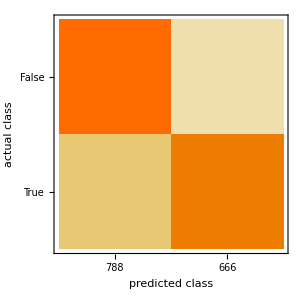

```mathematica
TestRasterizeClassifier["ConfusionMatrixPlot"]
```

```mathematica
easy to tell when it doesn't halt - hard to tell when it does halt (converse to expected)
```